```mathematica
G[x_,sigma_]:=Exp[-x^2/2/sigma^2]/sigma/Sqrt[2*Pi]
```

```mathematica
L[x_,gamma_]:=gamma/Pi/(x^2+gamma^2)
```

```mathematica
V[x_,sigma_,gamma_]:=NIntegrate[G[y,sigma]*L[x-y,gamma],{y,-Infinity,Infinity}]
```

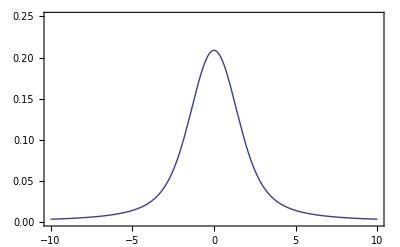

```mathematica
Plot[V[x,1,1],{x,-10,10},PlotRange->{0,0.25},Frame->True,Axes->None]
```

```mathematica
NIntegrate[G[y,sigma]*L[x-y,gamma],{y,-Infinity,Infinity}]
```

NIntegrate::inumr: The integrand ⅇ^-y^2/2\ sigma^2\ gamma/√2\ π^3/2\ sigma\ (gamma^2 + (x - y)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

NIntegrate[G[y,sigma] L[x-y,gamma],{y,-∞,∞}]